```mathematica
Simplify[Solve[x*(1+(1-x))-r== 0,x]]
Simplify[Solve[x*(1+a(1-g))-p+k== x*(1+(1-x))-r,x]]
```

```mathematica
Simplify[Solve[x*(1+(1-x))-r== 0,x]]
```

{{x→1-√(1-r)},{x→1+√(1-r)}}

```mathematica
Simplify[Solve[x*(1+a(√(1-r)))-p+k== x*(1+(√(1-r)))-r,x]]
```

{{x→(-k+p-r)/((-1+a) √(1-r))}}

```mathematica
Simplify[Solve[{D[p(1-(-k+p-r)/((-1+a) √(1-r)))-k^2,p]==0,D[p(1-(-k+p-r)/((-1+a) √(1-r)))-k^2,k]==0},{k,p}]]
```

```mathematica
{{k->(1+a (-1+r)-(1+√(1-r)) r)/(4+√(1-r)+4 a (-1+r)-4 r),p->-(2 (-1+a) √(1-r) (-1+a+r-a r+√(1-r) r))/(4+√(1-r)+4 a (-1+r)-4 r)}}
```

```mathematica
Simplify[-(2 (-1+a) √(1-r) (-1+a+r-a r+√(1-r) r))/(4+√(1-r)+4 a (-1+r)-4 r)(1-(-(1+a (-1+r)-(1+√(1-r)) r)/(4+√(1-r)+4 a (-1+r)-4 r)+-(2 (-1+a) √(1-r) (-1+a+r-a r+√(1-r) r))/(4+√(1-r)+4 a (-1+r)-4 r)-r)/((-1+a) √(1-r)))-((1+a (-1+r)-(1+√(1-r)) r)/(4+√(1-r)+4 a (-1+r)-4 r))^2]
```

((1+a (-1+r)-(1+√(1-r)) r) (-1-4 √(1-r)-4 a^2 (1-r)^(3/2)-a (1+8 √(1-r)-4 r) (-1+r)+5 (1+√(1-r)) r-4 r^2))/(4+√(1-r)+4 a (-1+r)-4 r)^2

```mathematica
-(2 (-1+a) √(1-r) (-1+a+r-a r+√(1-r) r))/(4+√(1-r)+4 a (-1+r)-4 r)(-(2 (-1+a+r-a r+√(1-r) r))/(4+√(1-r)+4 a (-1+r)-4 r))-((1+a (-1+r)-(1+√(1-r)) r)/(4+√(1-r)+4 a (-1+r)-4 r))^2
```

```mathematica
Manipulate[Plot[{((1+a (-1+r)-(1+√(1-r)) r) (-1-4 √(1-r)-4 a^2 (1-r)^(3/2)-a (1+8 √(1-r)-4 r) (-1+r)+5 (1+√(1-r)) r-4 r^2))/(4+√(1-r)+4 a (-1+r)-4 r)^2,(-1+a)^2/(-5+4 a),(9a+a^2 4)/(27 a)},{r,0,1.1},PlotRange->{0,4}],{a,1.75,8}]
```

```mathematica
Simplify[Integrate[x(1+(√(1-r)))-r,{x,√(1-r),(-(1+a (-1+r)-(1+√(1-r)) r)/(4+√(1-r)+4 a (-1+r)-4 r)-(2 (-1+a) √(1-r) (-1+a+r-a r+√(1-r) r))/(4+√(1-r)+4 a (-1+r)-4 r)-r)/((-1+a) √(1-r))}]+
Integrate[x(1+a(√(1-r)))+(2 (-1+a) √(1-r) (-1+a+r-a r+√(1-r) r))/(4+√(1-r)+4 a (-1+r)-4 r)+(1+a (-1+r)-(1+√(1-r)) r)/(4+√(1-r)+4 a (-1+r)-4 r),{x,(-(1+a (-1+r)-(1+√(1-r)) r)/(4+√(1-r)+4 a (-1+r)-4 r)-(2 (-1+a) √(1-r) (-1+a+r-a r+√(1-r) r))/(4+√(1-r)+4 a (-1+r)-4 r)-r)/((-1+a) √(1-r)),1}]+((1+a (-1+r)-(1+√(1-r)) r) (-1-4 √(1-r)-4 a^2 (1-r)^(3/2)-a (1+8 √(1-r)-4 r) (-1+r)+5 (1+√(1-r)) r-4 r^2))/(4+√(1-r)+4 a (-1+r)-4 r)^2]
```

1/(2 (4+√(1-r)+4 a (-1+r)-4 r)^2)(-1+r) (2+12 √(1-r)-12 a^3 (1-r)^(3/2)-(33+59 √(1-r)) r+(34+60 √(1-r)) r^2+2 a^2 (-1+r) (-1-18 √(1-r)+4 (1+6 √(1-r)) r)-4 a (1+9 √(1-r)-(11+32 √(1-r)) r+(10+27 √(1-r)) r^2))

```mathematica
Manipulate[Plot[%260,{r,0,2},PlotRange->{0,6}],{a,1.25,13}]
```

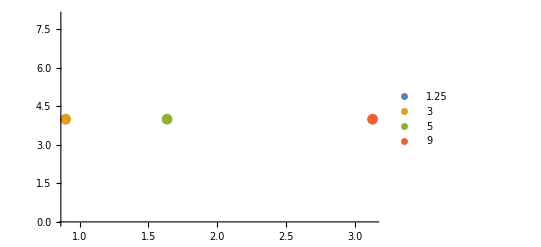

```mathematica
ListLinePlot[Table[{1/(2 (4+√(1-r)+4 a (-1+r)-4 r)^2)(-1+r) (2+12 √(1-r)-12 a^3 (1-r)^(3/2)-(33+59 √(1-r)) r+(34+60 √(1-r)) r^2+2 a^2 (-1+r) (-1-18 √(1-r)+4 (1+6 √(1-r)) r)-4 a (1+9 √(1-r)-(11+32 √(1-r)) r+(10+27 √(1-r)) r^2)),4},{a,{1.25,3,5,9}},{r,0,2}],Filling->Axis,PlotLegends->{1.25,3,5,9}]
```

```mathematica
Welfare[{a_}]:=1/(2 (4+√(1-r)+4 a (-1+r)-4 r)^2)(-1+r) (2+12 √(1-r)-12 a^3 (1-r)^(3/2)-(33+59 √(1-r)) r+(34+60 √(1-r)) r^2+2 a^2 (-1+r) (-1-18 √(1-r)+4 (1+6 √(1-r)) r)-4 a (1+9 √(1-r)-(11+32 √(1-r)) r+(10+27 √(1-r)) r^2))
```

```mathematica
parameters = {{1.25},{3},{5},{9}}
```

{{1.25},{3},{5},{9}}

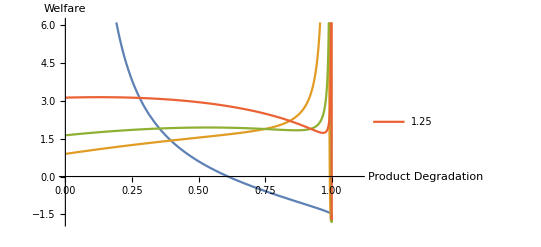

```mathematica
Plot[Welfare /@ parameters,{r,0,1.1},Evaluated->True,PlotLegends->{"1.25","3","5","9"} ,AxesLabel->{"Product Degradation","Welfare"}]
```

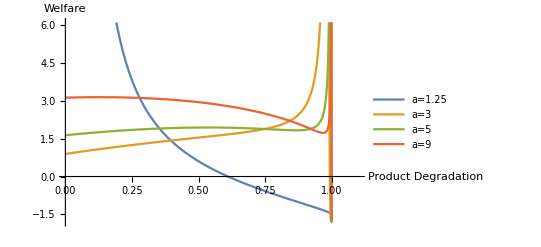

```mathematica
Welfare2=Plot[{1/(2 (4+√(1-r)+4 1.25 (-1+r)-4 r)^2)(-1+r) (2+12 √(1-r)-12 1.25^3 (1-r)^(3/2)-(33+59 √(1-r)) r+(34+60 √(1-r)) r^2+2 1.25^2 (-1+r) (-1-18 √(1-r)+4 (1+6 √(1-r)) r)-4 1.25 (1+9 √(1-r)-(11+32 √(1-r)) r+(10+27 √(1-r)) r^2)),1/(2 (4+√(1-r)+4 3 (-1+r)-4 r)^2)(-1+r) (2+12 √(1-r)-12 3^3 (1-r)^(3/2)-(33+59 √(1-r)) r+(34+60 √(1-r)) r^2+2 3^2 (-1+r) (-1-18 √(1-r)+4 (1+6 √(1-r)) r)-4 3 (1+9 √(1-r)-(11+32 √(1-r)) r+(10+27 √(1-r)) r^2)),1/(2 (4+√(1-r)+4 5 (-1+r)-4 r)^2)(-1+r) (2+12 √(1-r)-12 5^3 (1-r)^(3/2)-(33+59 √(1-r)) r+(34+60 √(1-r)) r^2+2 5^2 (-1+r) (-1-18 √(1-r)+4 (1+6 √(1-r)) r)-4 5 (1+9 √(1-r)-(11+32 √(1-r)) r+(10+27 √(1-r)) r^2)),1/(2 (4+√(1-r)+4 9 (-1+r)-4 r)^2)(-1+r) (2+12 √(1-r)-12 9^3 (1-r)^(3/2)-(33+59 √(1-r)) r+(34+60 √(1-r)) r^2+2 9^2 (-1+r) (-1-18 √(1-r)+4 (1+6 √(1-r)) r)-4 9 (1+9 √(1-r)-(11+32 √(1-r)) r+(10+27 √(1-r)) r^2))},{r,0,1.1},Evaluated->True,PlotLegends->{"a=1.25","a=3","a=5","a=9"} ,AxesLabel->{"Product Degradation","Welfare"}]
```

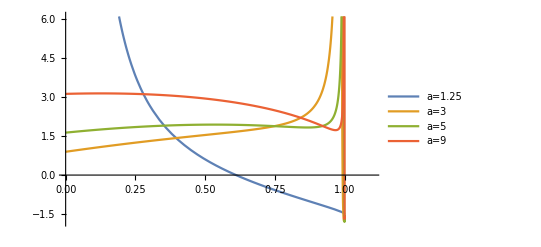

```mathematica
Welfare2=Plot[{1/(2 (4+√(1-r)+4 1.25 (-1+r)-4 r)^2)(-1+r) (2+12 √(1-r)-12 1.25^3 (1-r)^(3/2)-(33+59 √(1-r)) r+(34+60 √(1-r)) r^2+2 1.25^2 (-1+r) (-1-18 √(1-r)+4 (1+6 √(1-r)) r)-4 1.25 (1+9 √(1-r)-(11+32 √(1-r)) r+(10+27 √(1-r)) r^2)),1/(2 (4+√(1-r)+4 3 (-1+r)-4 r)^2)(-1+r) (2+12 √(1-r)-12 3^3 (1-r)^(3/2)-(33+59 √(1-r)) r+(34+60 √(1-r)) r^2+2 3^2 (-1+r) (-1-18 √(1-r)+4 (1+6 √(1-r)) r)-4 3 (1+9 √(1-r)-(11+32 √(1-r)) r+(10+27 √(1-r)) r^2)),1/(2 (4+√(1-r)+4 5 (-1+r)-4 r)^2)(-1+r) (2+12 √(1-r)-12 5^3 (1-r)^(3/2)-(33+59 √(1-r)) r+(34+60 √(1-r)) r^2+2 5^2 (-1+r) (-1-18 √(1-r)+4 (1+6 √(1-r)) r)-4 5 (1+9 √(1-r)-(11+32 √(1-r)) r+(10+27 √(1-r)) r^2)),1/(2 (4+√(1-r)+4 9 (-1+r)-4 r)^2)(-1+r) (2+12 √(1-r)-12 9^3 (1-r)^(3/2)-(33+59 √(1-r)) r+(34+60 √(1-r)) r^2+2 9^2 (-1+r) (-1-18 √(1-r)+4 (1+6 √(1-r)) r)-4 9 (1+9 √(1-r)-(11+32 √(1-r)) r+(10+27 √(1-r)) r^2))},{r,0,1.1},Evaluated->True,PlotLegends->{"a=1.25","a=3","a=5","a=9"} ,AxesLabel->{"r","Welfare"}];
Export["Welfare2.jpg",Welfare2]
```

Welfare2.jpg

```mathematica
SystemOpen["Welfare1.jpg"]
```

```mathematica
ExpandFileName["Welfare1.jpg"]
```

C:\Users\DavidEttinger02\Documents\Welfare1.jpg

```mathematica
N[12/7]
```

1.71429

```mathematica
Simplify[Solve[x*(1+a)-p+k== x*(1+1),x]]
```

{{x→(-k+p)/(-1+a)}}

```mathematica
Simplify[Solve[{D[p(1-(-k+p)/(-1+a))+o-k^2,p]==0,D[p(1-(-k+p)/(-1+a))+o-k^2,k]==0},{k,p}]]
```

{{k→(-1+a)/(-5+4 a),p→(2 (-1+a)^2)/(-5+4 a)}}

```mathematica
Simplify[(2 (-1+a)^2)/(-5+4 a)*(1-(-(-1+a)/(-5+4 a)+(2 (-1+a)^2)/(-5+4 a))/(-1+a))+o-((-1+a)/(-5+4 a))^2]
```

(1+a^2-5 o+a (-2+4 o))/(-5+4 a)

```mathematica
Simplify[(2 (-1+a)^2)/(-5+4 a)*(1-(-(-1+a)/(-5+4 a)+(2 (-1+a)^2)/(-5+4 a))/(-1+a))-((-1+a)/(-5+4 a))^2]
```

(-1+a)^2/(-5+4 a)

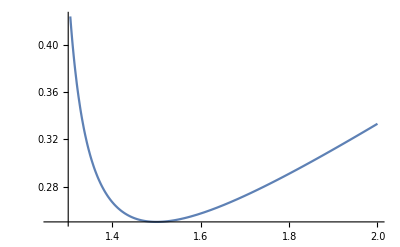

```mathematica
Plot[(a-1)^2/(4a-5),{a,1.26,2}]
```

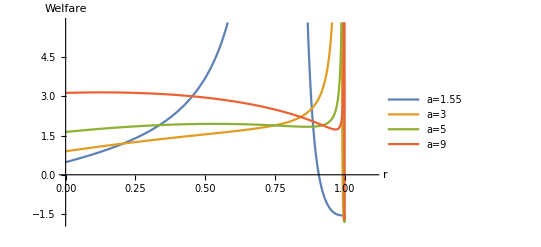

```mathematica
Welfare3=Plot[{1/(2 (4+√(1-r)+4 1.55 (-1+r)-4 r)^2)(-1+r) (2+12 √(1-r)-12 1.55^3 (1-r)^(3/2)-(33+59 √(1-r)) r+(34+60 √(1-r)) r^2+2 1.55^2 *(-1+r) (-1-18 √(1-r)+4 (1+6 √(1-r)) r)-4 1.55* (1+9 √(1-r)-(11+32 √(1-r)) r+(10+27 √(1-r)) r^2)),1/(2 (4+√(1-r)+4 3 (-1+r)-4 r)^2)(-1+r) (2+12 √(1-r)-12 3^3 (1-r)^(3/2)-(33+59 √(1-r)) r+(34+60 √(1-r)) r^2+2 3^2 (-1+r) (-1-18 √(1-r)+4 (1+6 √(1-r)) r)-4 3 (1+9 √(1-r)-(11+32 √(1-r)) r+(10+27 √(1-r)) r^2)),1/(2 (4+√(1-r)+4 5 (-1+r)-4 r)^2)(-1+r) (2+12 √(1-r)-12 5^3 (1-r)^(3/2)-(33+59 √(1-r)) r+(34+60 √(1-r)) r^2+2 5^2 (-1+r) (-1-18 √(1-r)+4 (1+6 √(1-r)) r)-4 5 (1+9 √(1-r)-(11+32 √(1-r)) r+(10+27 √(1-r)) r^2)),1/(2 (4+√(1-r)+4 9 (-1+r)-4 r)^2)(-1+r) (2+12 √(1-r)-12 9^3 (1-r)^(3/2)-(33+59 √(1-r)) r+(34+60 √(1-r)) r^2+2 9^2 (-1+r) (-1-18 √(1-r)+4 (1+6 √(1-r)) r)-4 9 (1+9 √(1-r)-(11+32 √(1-r)) r+(10+27 √(1-r)) r^2))},{r,0,1.1},Evaluated->True,PlotLegends->{"a=1.55","a=3","a=5","a=9"} ,AxesLabel->{"r","Welfare"}]
```

```mathematica
Export["Welfare3.jpg",Welfare3]
```

Welfare3.jpg

```mathematica
SystemOpen[DirectoryName[AbsoluteFileName["Welfare3.jpg"]]]
```

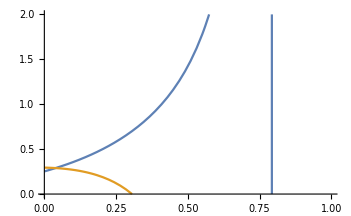

```mathematica
Plot[{-(2 (-1+1.55) √(1-r) (-1+1.55+r-1.55 r+√(1-r) r))/(4+√(1-r)+4 1.55 (-1+r)-4 r)(-(2 (-1+1.55+r-1.55*r+√(1-r) r))/(4+√(1-r)+4 1.55 (-1+r)-4 r))-((1+1.55*(-1+r)-(1+√(1-r)) r)/(4+√(1-r)+4 1.55 (-1+r)-4 r))^2,-(2 (-1+1.55) √(1-r) (-1+1.55+r-1.55*r+√(1-r) r))/(4+√(1-r)+4 1.55 (-1+r)-4 r)-((1+1.55 (-1+r)-(1+√(1-r)) r)/(4+√(1-r)+4 1.55 (-1+r)-4 r))^2},{r,0,1},PlotRange->{0,2}]
```

```mathematica
Solve[-(2 (-1+1.55+r-1.55*r+√(1-r) r))/(4+√(1-r)+4 1.55 (-1+r)-4 r)==1,r]
```

{{r→0.0391315}}

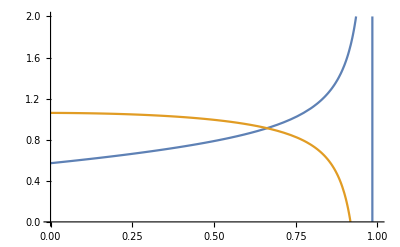

```mathematica
Plot[{-(2 (-1+3) √(1-r) (-1+3+r-3 r+√(1-r) r))/(4+√(1-r)+4 3 (-1+r)-4 r)(-(2 (-1+3+r-3*r+√(1-r) r))/(4+√(1-r)+4 3(-1+r)-4 r))-((1+3*(-1+r)-(1+√(1-r)) r)/(4+√(1-r)+4 3 (-1+r)-4 r))^2,-(2 (-1+3) √(1-r) (-1+3+r-3*r+√(1-r) r))/(4+√(1-r)+4 3(-1+r)-4 r)-((1+3 (-1+r)-(1+√(1-r)) r)/(4+√(1-r)+4 3 (-1+r)-4 r))^2},{r,0,1},PlotRange->{0,2}]
```

```mathematica
Solve[(-(2 (-1+3+r-3*r+√(1-r) r))/(4+√(1-r)+4 3(-1+r)-4 r))==1,r]
```

{{r→1/2 (-5+2 √10)}}

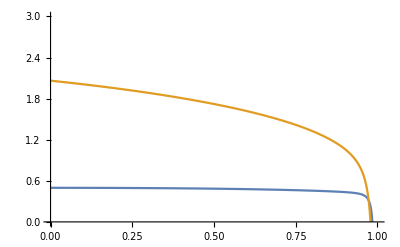

```mathematica
Plot[{-(2 (-1+3) √(1-r) (-1+5+r-5 r+√(1-r) r))/(4+√(1-r)+4 5 (-1+r)-4 r)(-(2 (-1+5+r-5*r+√(1-r) r))/(4+√(1-r)+4 5(-1+r)-4 r))-((1+5*(-1+r)-(1+√(1-r)) r)/(4+√(1-r)+4 5 (-1+r)-4 r))^2,-(2 (-1+5) √(1-r) (-1+5+r-5*r+√(1-r) r))/(4+√(1-r)+4 5(-1+r)-4 r)-((1+5 (-1+r)-(1+√(1-r)) r)/(4+√(1-r)+4 5 (-1+r)-4 r))^2},{r,0,1},PlotRange->{0,3}]
```

```mathematica
Solve[(-(2 (-1+5+r-5*r+√(1-r) r))/(4+√(1-r)+4 5(-1+r)-4 r))==1 ,r]
```

{{r→1/2 (-17+4 √22)}}

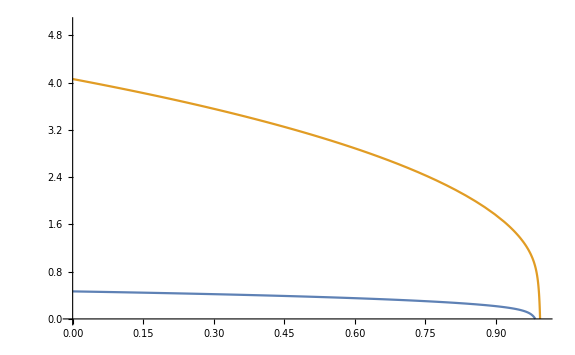

```mathematica
Plot[{-(2 (-1+3) √(1-r) (-1+9+r-9 r+√(1-r) r))/(4+√(1-r)+4 9 (-1+r)-4 r)(-(2 (-1+9+r-9*r+√(1-r) r))/(4+√(1-r)+4 9(-1+r)-4 r))-((1+9*(-1+r)-(1+√(1-r)) r)/(4+√(1-r)+4 9 (-1+r)-4 r))^2,-(2 (-1+9) √(1-r) (-1+9+r-9*r+√(1-r) r))/(4+√(1-r)+4 9(-1+r)-4 r)-((1+9(-1+r)-(1+√(1-r)) r)/(4+√(1-r)+4 9 (-1+r)-4 r))^2},{r,0,1},PlotRange->{0,5}]
```

```mathematica
Solve[(-(2 (-1+9+r-9*r+√(1-r) r))/(4+√(1-r)+4 9(-1+r)-4 r))==1 ,r]
```

{{r→1/2 (-65+8 √70)}}

```mathematica
Show[{Plot[{f[x],f[Pi/15],f[Pi/15]/Sqrt[2]},{x,0.1,0.3},PlotRange->All,Frame->True,Axes->False],ParametricPlot[{{Pi/15+1/20,u},{Pi/15-1/20,u}},{u,0,9000},PlotStyle->Black]}]
```

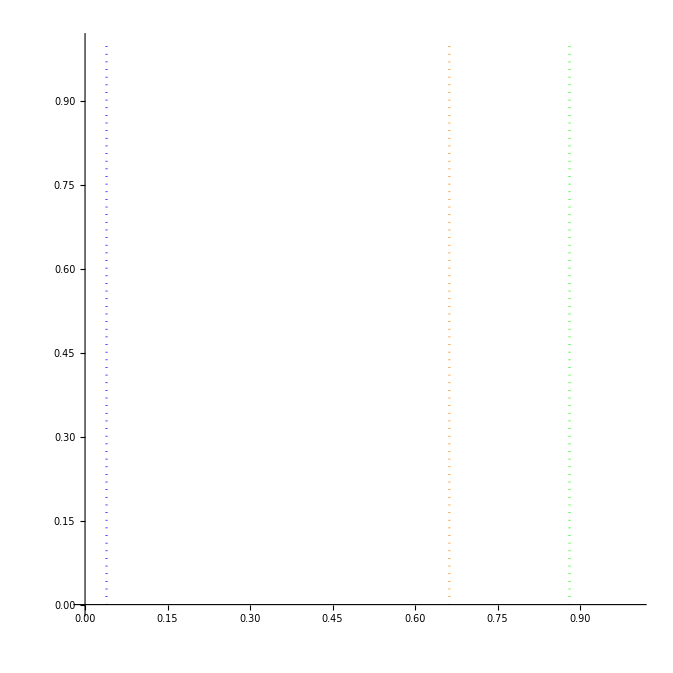

```mathematica
ParametricPlot[{{0.03913146158482558,r},{1/2 (-5+2 √10),r},{1/2 (-17+4 √22),r}},{r,0,1},PlotStyle->{{ Blue,Dotted},{Orange,Dotted},{Green,Dotted}},PlotRange->{0,1}]
```

```mathematica
Welfare4=Show[Plot[{1/(2 (4+√(1-r)+4 1.55 (-1+r)-4 r)^2)(-1+r) (2+12 √(1-r)-12 1.55^3 (1-r)^(3/2)-(33+59 √(1-r)) r+(34+60 √(1-r)) r^2+2 1.55^2 *(-1+r) (-1-18 √(1-r)+4 (1+6 √(1-r)) r)-4 1.55* (1+9 √(1-r)-(11+32 √(1-r)) r+(10+27 √(1-r)) r^2)),1/(2 (4+√(1-r)+4 3 (-1+r)-4 r)^2)(-1+r) (2+12 √(1-r)-12 3^3 (1-r)^(3/2)-(33+59 √(1-r)) r+(34+60 √(1-r)) r^2+2 3^2 (-1+r) (-1-18 √(1-r)+4 (1+6 √(1-r)) r)-4 3 (1+9 √(1-r)-(11+32 √(1-r)) r+(10+27 √(1-r)) r^2)),1/(2 (4+√(1-r)+4 5 (-1+r)-4 r)^2)(-1+r) (2+12 √(1-r)-12 5^3 (1-r)^(3/2)-(33+59 √(1-r)) r+(34+60 √(1-r)) r^2+2 5^2 (-1+r) (-1-18 √(1-r)+4 (1+6 √(1-r)) r)-4 5 (1+9 √(1-r)-(11+32 √(1-r)) r+(10+27 √(1-r)) r^2)),1/(2 (4+√(1-r)+4 9 (-1+r)-4 r)^2)(-1+r) (2+12 √(1-r)-12 9^3 (1-r)^(3/2)-(33+59 √(1-r)) r+(34+60 √(1-r)) r^2+2 9^2 (-1+r) (-1-18 √(1-r)+4 (1+6 √(1-r)) r)-4 9 (1+9 √(1-r)-(11+32 √(1-r)) r+(10+27 √(1-r)) r^2))},{r,0,1.1},Evaluated->True,PlotLegends->{"a=1.55","a=3","a=5","a=9"} ,AxesLabel->{"r","Welfare"},PlotRange->{0,6}],ParametricPlot[{{0.03913146158482558,r},{1/2 (-5+2 √10),r},{1/2 (-17+4 √22),r}},{r,0,1},PlotStyle->{{ Blue,Dotted},{Orange,Dotted},{Green,Dotted}},PlotRange->{0,1}]]
```

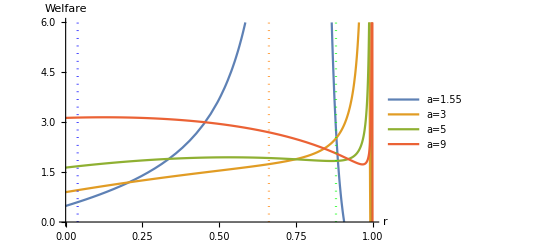

```mathematica
Welfare3 = Show[Plot[{1/(2 (4+√(1-r)+4 1.55 (-1+r)-4 r)^2)(-1+r) (2+12 √(1-r)-12 1.55^3 (1-r)^(3/2)-(33+59 √(1-r)) r+(34+60 √(1-r)) r^2+2 1.55^2 *(-1+r) (-1-18 √(1-r)+4 (1+6 √(1-r)) r)-4 1.55* (1+9 √(1-r)-(11+32 √(1-r)) r+(10+27 √(1-r)) r^2)),1/(2 (4+√(1-r)+4 3 (-1+r)-4 r)^2)(-1+r) (2+12 √(1-r)-12 3^3 (1-r)^(3/2)-(33+59 √(1-r)) r+(34+60 √(1-r)) r^2+2 3^2 (-1+r) (-1-18 √(1-r)+4 (1+6 √(1-r)) r)-4 3 (1+9 √(1-r)-(11+32 √(1-r)) r+(10+27 √(1-r)) r^2)),1/(2 (4+√(1-r)+4 5 (-1+r)-4 r)^2)(-1+r) (2+12 √(1-r)-12 5^3 (1-r)^(3/2)-(33+59 √(1-r)) r+(34+60 √(1-r)) r^2+2 5^2 (-1+r) (-1-18 √(1-r)+4 (1+6 √(1-r)) r)-4 5 (1+9 √(1-r)-(11+32 √(1-r)) r+(10+27 √(1-r)) r^2)),1/(2 (4+√(1-r)+4 9 (-1+r)-4 r)^2)(-1+r) (2+12 √(1-r)-12 9^3 (1-r)^(3/2)-(33+59 √(1-r)) r+(34+60 √(1-r)) r^2+2 9^2 (-1+r) (-1-18 √(1-r)+4 (1+6 √(1-r)) r)-4 9 (1+9 √(1-r)-(11+32 √(1-r)) r+(10+27 √(1-r)) r^2))},{r,0,1.1},Evaluated->True,PlotLegends->{"a=1.55","a=3","a=5","a=9"} ,AxesLabel->{"r","Welfare"},PlotRange->{0,6}],ParametricPlot[{{0.03913146158482558,r},{1/2 (-5+2 √10),r},{1/2 (-17+4 √22),r}},{r,0,6},PlotStyle->{{ Blue,Dotted},{Orange,Dotted},{Green,Dotted}},PlotRange->{{0,1.1},{0,6}}]]
```

```mathematica
Export["Welfare3.jpg",Welfare3]
```

```mathematica
Simplify[Solve[{D[p(1-(-k+p-r)/m)-k^2,p]==0,D[p(1-(-k+p-r)/m)-k^2,k]==0},{k,p}]]
```

{{k→(m+r)/(-1+4 m),p→(2 m (m+r))/(-1+4 m)}}

```mathematica
Simplify[((2 m (m+r))/(-1+4 m))(1-(-((m+r)/(-1+4 m))+((2 m (m+r))/(-1+4 m))-r)/m)-((m+r)/(-1+4 m))^2]
```

(m+r)^2/(-1+4 m)

```mathematica
Simplify[(4+√(1-r)+4 a (-1+r)-4 r)^2]
```

(4+√(1-r)+4 a (-1+r)-4 r)^2

```mathematica
-1+4 m
```

```mathematica
Integrate[((a-1)√(1-r)+r)^2/(-1+4*(a-1)√(1-r))*,r]
```

```mathematica
NormalDistribution
```

NormalDistribution

```mathematica
Information[NormalDistribution]
```

System`NormalDistribution

Attributes[NormalDistribution]={Protected,ReadProtected}

```mathematica
PDF[NormalDistribution[μ,σ],r]
```

(ⅇ^(-(r-μ)^2/(2 σ^2)))/(√(2 π) σ)

```mathematica
Integrate[((a-1)√(1-r)+r)^2/(-1+4*(a-1)√(1-r))*,r]
```

```mathematica
Simplify[Solve[D[((a-1)√(1-r)+r)^2/(-1+4*(a-1)√(1-r)),r]==0,r]]
```

{{r→-1/2 (-1+a) (-1+a+√(5-2 a+a^2))},{r→1/2 (-1+a) (1-a+√(5-2 a+a^2))},{r→-(-23+46 a-19 a^2-4 a^3+a^4+√((2-2 a+a^2)^2 (-14+28 a-10 a^2-4 a^3+a^4)))/(18 (-1+a)^2)},{r→(23-46 a+19 a^2+4 a^3-a^4+√((2-2 a+a^2)^2 (-14+28 a-10 a^2-4 a^3+a^4)))/(18 (-1+a)^2)}}

```mathematica
-1/2 (-1+a) (-1+a+√(5-2 a+a^2))
```

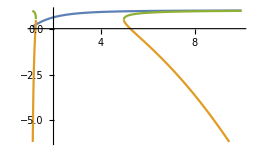

```mathematica
Plot[{1/2 (-1+a) (1-a+√(5-2 a+a^2)),-(-23+46 a-19 a^2-4 a^3+a^4+√((2-2 a+a^2)^2 (-14+28 a-10 a^2-4 a^3+a^4)))/(18 (-1+a)^2),(23-46 a+19 a^2+4 a^3-a^4+√((2-2 a+a^2)^2 (-14+28 a-10 a^2-4 a^3+a^4)))/(18 (-1+a)^2)},{a,1.1,10}]
```

```mathematica
Integrate[((a-1)√(1-r)+r)^2/(-1+4*(a-1)√(1-r))*(ⅇ^(-((r-1/2 (-1+a) (1-a+√(5-2 a+a^2)))^2)/(2 σ^2)))/(√(2 π) σ),{r,0,2}]
```

$Aborted

```mathematica
Simplify[(ⅇ^(-((r-1/2 (-1+a) (1-a+√(5-2 a+a^2)))^2)/(2 σ^2)))/(√(2 π) σ)]
```

(ⅇ^(-((-1/2 (-1+a) (1-a+√(5-2 a+a^2))+r)^2)/(2 σ^2)))/(√(2 π) σ)

```mathematica
NormalDistribution[{0,∞},NormalDistribution[]];
```

```mathematica
𝒟=NormalDistribution[{-∞,0.5},𝒹=CauchyDistribution[0,1]];
```

```mathematica
Plot[NormalDistribution[{0,∞},NormalDistribution[]]]
```

Plot[NormalDistribution[{0,∞},NormalDistribution[]]]

```mathematica
NormalDistribution[{0,∞},NormalDistribution[0,1]]
```

NormalDistribution[{0,∞},NormalDistribution[0,1]]

```mathematica
𝒟=TruncatedDistribution[{0,∞},𝒹=NormalDistribution[m,s]];
```

```mathematica
Plot[{Legended[PDF[𝒹,x],"𝒹"],Legended[PDF[𝒟,x],"𝒟"]},{x,-2,2},Filling->Axis]
```

```mathematica
Integrate[((a-1)√(1-r)+r)^2/(-1+4*(a-1)√(1-r))*1/e,r]
```

```mathematica
Manipulate[Plot3D[-1/(30720 (-1+a)^6 e)(60 (-1+a) (19-40 a+20 a^2)^2 √(1-r)+320 (-1+a)^3 (-23+16 a+56 a^2-64 a^3+16 a^4) (1-r)^(3/2)+3072 (-1+a)^5 (1-r)^(5/2)-120 (-1+a)^2 (105-496 a+824 a^2-576 a^3+144 a^4) (-1+r)-960 (-1+a)^4 (7-16 a+8 a^2) (-1+r)^2+15 (19-40 a+20 a^2)^2 Log[1+4 √(1-r)-4 a √(1-r)]),{e,0,2},{r,0.1,10}],{a,1.5,10}]
```

```mathematica
Simplify[Integrate[((a-1)√(1-r)+r)^2/(-1+4*(a-1)√(1-r))*1/e,r]]
```

-1/(30720 (-1+a)^6 e)(60 (-1+a) (19-40 a+20 a^2)^2 √(1-r)+320 (-1+a)^3 (-23+16 a+56 a^2-64 a^3+16 a^4) (1-r)^(3/2)+3072 (-1+a)^5 (1-r)^(5/2)-120 (-1+a)^2 (105-496 a+824 a^2-576 a^3+144 a^4) (-1+r)-960 (-1+a)^4 (7-16 a+8 a^2) (-1+r)^2+15 (19-40 a+20 a^2)^2 Log[1+4 √(1-r)-4 a √(1-r)])

```mathematica
Simplify[D[((a-1)√(1-r)+r)/(-1+4 ((a-1)√(1-r))),r]]
```

(-9+a (9-4 r)-2 √(1-r)+4 r)/(2 (1+4 √(1-r)-4 a √(1-r))^2 √(1-r))

```mathematica
((a-1)√(1-r)+r)/(-1+4 ((a-1)√(1-r)))
```

((-1+a) √(1-r)+r)/(-1+4 (-1+a) √(1-r))

```mathematica
Manipulate[Plot[{((-1+a) √(1-r)+r)/(-1+4 (-1+a) √(1-r)),.3333,(a-1)/(4*a-5)},{r,0,1.1},PlotRange->{0,1}],{a,1.5,8}]
```

```mathematica
Simplify[Solve[x*(t+(1-t)a(1-g))-p+k== 0,x]]
```

{{x→(-k+p)/(a (-1+g) (-1+t)+t)}}

```mathematica
Simplify[Solve[x*(t+(1-t)a(1-x))-p+k== 0,x]]
```

{{x→-(a+t-a t+√(-4 a (k-p) (-1+t)+(a+t-a t)^2))/(2 a (-1+t))},{x→(-a-t+a t+√(-4 a (k-p) (-1+t)+(a+t-a t)^2))/(2 a (-1+t))}}

```mathematica
Simplify[Solve[{D[p*(1-(a+t-a t+√(-4 a (k-p) (-1+t)+(a+t-a t)^2))/(2 a (-1+t)))-k^2,p]==0,D[p*(1-(a+t-a t+√(-4 a (k-p) (-1+t)+(a+t-a t)^2))/(2 a (-1+t)))-k^2,k]==0,1≥ t≥ 0,p≥ 0,a≥ 0,k≥ 0},{p,k}]]
```

{{p→ConditionalExpression[1/(72 a (-1+t))(1-12 a (-1+t)+4 t+√(48 a^2 (-1+t)^2+(1+4 t)^2+24 a (1+t-2 t^2))) (1-12 a (-1+t)+4 t+√(48 a^2 (-1+t)^2+(1+4 t)^2+24 a (1+t-2 t^2))-2 √(2+57 a^2 (-1+t)^2+10 t+17 t^2+2 √(48 a^2 (-1+t)^2+(1+4 t)^2+24 a (1+t-2 t^2))+2 t √(48 a^2 (-1+t)^2+(1+4 t)^2+24 a (1+t-2 t^2))-6 a (-1+t) (5+9 t+√(48 a^2 (-1+t)^2+(1+4 t)^2+24 a (1+t-2 t^2))))),a>0&&0<t<1],k→ConditionalExpression[-(1-12 a (-1+t)+4 t+√(48 a^2 (-1+t)^2+(1+4 t)^2+24 a (1+t-2 t^2)))/(24 a (-1+t)),a>0&&0<t<1]}}

```mathematica
Simplify[1/(72 a (-1+t))(1-12 a (-1+t)+4 t+√(48 a^2 (-1+t)^2+(1+4 t)^2+24 a (1+t-2 t^2))) (1-12 a (-1+t)+4 t+√(48 a^2 (-1+t)^2+(1+4 t)^2+24 a (1+t-2 t^2))-2 √(2+57 a^2 (-1+t)^2+10 t+17 t^2+2 √(48 a^2 (-1+t)^2+(1+4 t)^2+24 a (1+t-2 t^2))+2 t √(48 a^2 (-1+t)^2+(1+4 t)^2+24 a (1+t-2 t^2))-6 a (-1+t) (5+9 t+√(48 a^2 (-1+t)^2+(1+4 t)^2+24 a (1+t-2 t^2)))))*(1-1/(2 a (-1+t))(a+t-a t+√(-4 a (-(1-12 a (-1+t)+4 t+√(48 a^2 (-1+t)^2+(1+4 t)^2+24 a (1+t-2 t^2)))/(24 a (-1+t))-1/(72 a (-1+t))(1-12 a (-1+t)+4 t+√(48 a^2 (-1+t)^2+(1+4 t)^2+24 a (1+t-2 t^2))) (1-12 a (-1+t)+4 t+√(48 a^2 (-1+t)^2+(1+4 t)^2+24 a (1+t-2 t^2))-2 √(2+57 a^2 (-1+t)^2+10 t+17 t^2+2 √(48 a^2 (-1+t)^2+(1+4 t)^2+24 a (1+t-2 t^2))+2 t √(48 a^2 (-1+t)^2+(1+4 t)^2+24 a (1+t-2 t^2))-6 a (-1+t) (5+9 t+√(48 a^2 (-1+t)^2+(1+4 t)^2+24 a (1+t-2 t^2)))))) (-1+t)+(a+t-a t)^2)))-(-(1-12 a (-1+t)+4 t+√(48 a^2 (-1+t)^2+(1+4 t)^2+24 a (1+t-2 t^2)))/(24 a (-1+t)))^2]
```

1/(576 a^2 (-1+t)^2)(1-12 a (-1+t)+4 t+√(48 a^2 (-1+t)^2+(1+4 t)^2+24 a (1+t-2 t^2))) (-1+12 a (-1+t)-4 t-√(48 a^2 (-1+t)^2+(1+4 t)^2+24 a (1+t-2 t^2))+2/3 (1-12 a (-1+t)+4 t+√(48 a^2 (-1+t)^2+(1+4 t)^2+24 a (1+t-2 t^2))-2 √(2+57 a^2 (-1+t)^2+10 t+17 t^2+2 √(48 a^2 (-1+t)^2+(1+4 t)^2+24 a (1+t-2 t^2))+2 t √(48 a^2 (-1+t)^2+(1+4 t)^2+24 a (1+t-2 t^2))-6 a (-1+t) (5+9 t+√(48 a^2 (-1+t)^2+(1+4 t)^2+24 a (1+t-2 t^2))))) (-18 a-6 t+18 a t-6 √((a+t-a t)^2+1/18 (1-12 a (-1+t)+4 t+√(48 a^2 (-1+t)^2+(1+4 t)^2+24 a (1+t-2 t^2))) (4-12 a (-1+t)+4 t+√(48 a^2 (-1+t)^2+(1+4 t)^2+24 a (1+t-2 t^2))-2 √(2+57 a^2 (-1+t)^2+10 t+17 t^2+2 √(48 a^2 (-1+t)^2+(1+4 t)^2+24 a (1+t-2 t^2))+2 t √(48 a^2 (-1+t)^2+(1+4 t)^2+24 a (1+t-2 t^2))-6 a (-1+t) (5+9 t+√(48 a^2 (-1+t)^2+(1+4 t)^2+24 a (1+t-2 t^2))))))))

```mathematica
Manipulate[Plot[{%284,1/(72 a (-1+t))(1-12 a (-1+t)+4 t+√(48 a^2 (-1+t)^2+(1+4 t)^2+24 a (1+t-2 t^2))) (1-12 a (-1+t)+4 t+√(48 a^2 (-1+t)^2+(1+4 t)^2+24 a (1+t-2 t^2))-2 √(2+57 a^2 (-1+t)^2+10 t+17 t^2+2 √(48 a^2 (-1+t)^2+(1+4 t)^2+24 a (1+t-2 t^2))+2 t √(48 a^2 (-1+t)^2+(1+4 t)^2+24 a (1+t-2 t^2))-6 a (-1+t) (5+9 t+√(48 a^2 (-1+t)^2+(1+4 t)^2+24 a (1+t-2 t^2)))))-((1-12 a (-1+t)+4 t+√(48 a^2 (-1+t)^2+(1+4 t)^2+24 a (1+t-2 t^2)))/(24 a (-1+t)))^2},{t,0,1}],{a,1,100}]
```

```mathematica
Simplify[Solve[x*(1+a(1-x))-p+k== 0,x]]
```

{{x→(1+a-√(1+a^2+a (2+4 k-4 p)))/(2 a)},{x→(1+a+√(1+a^2+a (2+4 k-4 p)))/(2 a)}}

```mathematica
Simplify[Solve[{D[p*(1-(1+a-√(1+a^2+a (2+4 k-4 p)))/(2 a))-k^2,p]==0,D[p*(1-(1+a-√(1+a^2+a (2+4 k-4 p)))/(2 a))-k^2,k]==0,1≥ t≥ 0,p≥ 0,a≥ 0,k≥ 0},{p,k}]]
```

{{p→ConditionalExpression[(2 (3+a))/9,0<t<1&&a>0],k→ConditionalExpression[1/3,0<t<1&&a>0]}}

```mathematica
Simplify[Solve[x*((1-x))-p+k== 0,x]]
```

{{x→1/2 (1-√(1+4 k-4 p))},{x→1/2 (1+√(1+4 k-4 p))}}

```mathematica
Solve[{D[p*(1-1/2 (1-√(1+4 k-4 p)))-k^2,p]== 0,D[p*(1-1/2 (1-√(1+4 k-4 p)))-k^2,k]== 0,p≥ 0,k≥ 0},{p,k}]
```

{{p→5/9,k→5/12}}

```mathematica
Simplify[Solve[x-p+k== 0,x]]
```

{{x→-k+p}}

```mathematica
Solve[{D[p*(1-(-k+p))-k^2,p]== 0,D[p*(1-(-k+p))-k^2,k]== 0,p≥ 0,k≥ 0},{p,k}]
```

{{p→2/3,k→1/3}}

```mathematica
Simplify[Solve[x*(t+(1-t)(1-x))-p+k== 0,x]]
```

{{x→(1+√(1-4 k (-1+t)+4 p (-1+t)))/(2-2 t)},{x→(-1+√(1-4 k (-1+t)+4 p (-1+t)))/(2 (-1+t))}}

```mathematica
Simplify[Solve[{D[p*(1-(-1+√(1-4 k (-1+t)+4 p (-1+t)))/(2 (-1+t)))-k^2,p]== 0,D[p*(1-(-1+√(1-4 k (-1+t)+4 p (-1+t)))/(2 (-1+t)))-k^2,k]== 0,p≥ 0,k≥ 0,1>t>0},{p,k}]]
```

{{p→ConditionalExpression[1/(36 (-1+t))(25+40 t^2+5 √(25-32 t+16 t^2)-8 t (7+√(25-32 t+16 t^2))-√2 √(1312 t^4+245 (5+√(25-32 t+16 t^2))-32 t^3 (143+10 √(25-32 t+16 t^2))-28 t (163+27 √(25-32 t+16 t^2))+12 t^2 (557+67 √(25-32 t+16 t^2)))),0<t<1],k→ConditionalExpression[(5-8 t+√(25-32 t+16 t^2))/(24-24 t),0<t<1]}}